## Average over purity

Eigenvalues

## Normalisation factors

Eq 30

```mathematica
Sum[((1+r)/2)^l((1-r)/2)^(n-l)1/(2s+1),{l,n/2-s,n/2+s}]//FullSimplify
```

(2^(-1-n) (1-r^2)^(1/2 (n-2 s)) (-(1-r)^(1+2 s)+(1+r)^(1+2 s)))/(r+2 r s)

```mathematica
f[s_,n_,r_]:=(((1-r^2)/4)^(1/2 (n-2 s)) (-((1-r)/2)^(1+2 s)+((1+r)/2)^(1+2 s)))/(r(2s+1))
```

```mathematica
FullSimplify[Integrate[(((1-r^2)/4)^(1/2 (n-2 s)) (-((1-r)/2)^(1+2 s)+((1+r)/2)^(1+2 s)))/(r(2s+1)) 3*r^2,{r,0,1}],Assumptions->0<=2s≤n&&Element[n|2s, Integers]]
```

(6 Gamma[1+n/2-s] Gamma[2+n/2+s])/Gamma[4+n]

```mathematica
f[s_,n_]:=(6 Gamma[1+n/2-s] Gamma[2+n/2+s])/Gamma[4+n]
```

```mathematica
d[s_]:=2s+1
```

## Eigenvalues and signs

### Normalisation

Eq 44

```mathematica
R1[s_,n_]:=f[s+1/2,n+1]/f[s,n]
```

```mathematica
f[s+1/2,n+1]/f[s,n]//FullSimplify
```

1/2+s/(4+n)

```mathematica
R2[s_,n_]:=f[s-1/2,n+1]/f[s,n]
```

```mathematica
f[s-1/2,n+1]/f[s,n]//FullSimplify
```

(2+n-2 s)/(8+2 n)

### 1x1 case

Normalised eigenvalues

#### case a)

```mathematica
Λ1[s_,t_,n_]:=R1[s,n]-R1[t,n]
```

```mathematica
Λ1[s,t,n]//FullSimplify
```

(s-t)/(4+n)

-> positive sign if r1>r2, negative if r1<r2

#### case b)

```mathematica
Λ2[s_,t_,n_]:=R1[s,n]-R2[t,n]
```

```mathematica
Λ2[s,t,n]//FullSimplify
```

(1+s+t)/(4+n)

-> postitive sign

#### case c)

```mathematica
Λ3[s_,t_,n_]:=R2[s,n]-R1[t,n]
```

```mathematica
Λ3[s,t,n]//FullSimplify
```

-(1+s+t)/(4+n)

-> negative sign

#### 2x2 case

Wigner 6j squared

```mathematica
W[s_,t_,q_]:=((1/2+q-s+t)(1/2+q+s-t))/((2s+1)(2t+1))
```

```mathematica
g[s_,t_,n_]:=R1[s,n]-R2[s,n]
```

```mathematica
a[s_,t_,n_]:=1/2(R1[s,n]+R2[s,n] -R1[t,n]-R2[t,n] )
```

```mathematica
a[s,t,n]//FullSimplify
```

0

```mathematica
bc[s_,t_,q_,n_]:=1/4(g[s,t,n]+g[t,s,n])^2-g[s,t,n]g[t,s,n]W[s,t,q]
```

```mathematica
Sqrt[bc[s,t,q,n]]//FullSimplify
```

1/2 √((3-4 q (1+q)+8 s (1+s)+8 t (1+t))/(4+n)^2)

```mathematica
Eigen1[s_,t_,q_,n_]:=+1/2 √((3-4 q (1+q)+8 s (1+s)+8 t (1+t))/(4+n)^2)
```

```mathematica
Eigen2[s_,t_,q_,n_]:=-1/2 √((3-4 q (1+q)+8 s (1+s)+8 t (1+t))/(4+n)^2)
```

```mathematica
Eigen1[s,t,q,n]
```

1/2 √((3-4 q (1+q)+8 s (1+s)+8 t (1+t))/(4+n)^2)

-> postitive sign

```mathematica
Eigen2[s,t,q,n]//FullSimplify
```

-1/2 √((3-4 q (1+q)+8 s (1+s)+8 t (1+t))/(4+n)^2)

-> negative sign

Asymptotic error probability

## Perr

multiplicity of the irreps

```mathematica
mult[s_,n_]:= (n!)/(((n-2s)/2)!((n+2s)/2+1)!)(2s+1)
```

multiplicity factor

```mathematica
Fmult[s_,t_,n_]:= mult[s,n]mult[t,n]f[s,n]f[t,n]//FullSimplify
```

```mathematica
Fmult[s,t,n]
```

(36 (1+2 s) (1+2 t))/((1+n)^2 (2+n)^2 (3+n)^2)

In general the error probability is (for n odd)

```mathematica
Perr[n_]:=1/2(1-(Sum[Fmult[s,t,n]((2(t+s+1/2)+1)Abs[Λ1[s,t,n]]+(2(t-s-1/2)+1)Abs[Λ3[s,t,n]]+Sum[(2q+1)(Abs[Eigen1[s,t,q,n]]+Abs[Eigen2[s,t,q,n]]),{q,t-s+1/2,s+t-1/2}]),{s,0, n/2},{t,s+1,n/2}]+
Sum[Fmult[s,t,n]((2(t+s+1/2)+1)Abs[Λ1[s,t,n]]+(2(-t+s-1/2)+1)Abs[Λ2[s,t,n]]+Sum[(2q+1)(Abs[Eigen1[s,t,q,n]]+Abs[Eigen2[s,t,q,n]]),{q,s-t+1/2,s+t-1/2}]),{t,0, n/2},{s,t+1,n/2}]+
Sum[Fmult[t,t,n]((2(2t+1/2)+1)Abs[Λ1[t,t,n]]+Sum[(2q+1)(Abs[Eigen1[t,t,q,n]]+Abs[Eigen2[t,t,q,n]]),{q,1/2,2t-1/2}]),{t,0, n/2}])/2)
```

with the results of the previous section we can instead calculate the contributions of Λ1, Λ2 and Eigen1

## Λ1

```mathematica
Sum[Fmult[s,t,n]d[s+t+1/2]Λ1[s,t,n],{s,0,n/2},{t,0,s-1}]//FullSimplify
```

(3 n^2 (4+n))/(16 (1+n)^2 (3+n)^2)

```mathematica
Λ1piece=Series[(3 n^2 (4+n))/(16 (1+n)^2 (3+n)^2),{n,Infinity,1}]
```

3/(16 n)+O[1/n]^2

## Λ2

```mathematica
Sum[Fmult[s,t,n]d[t-s-1/2]Λ2[s,t,n],{s,0,n/2},{t,s+1,n/2}]//FullSimplify
```

(3 n^2 (4+n))/(16 (1+n)^2 (3+n)^2)

```mathematica
Λ2piece=Series[(3 n^2 (4+n))/(16 (1+n)^2 (3+n)^2),{n,Infinity,1}]
```

3/(16 n)+O[1/n]^2

```mathematica
Λ2piece+Λ1piece
```

3/(8 n)+O[1/n]^2

## Eigen1

### Contribution b

#### MacLaurin approximation of the sum in q

```mathematica
int1q=Simplify[Fmult[s,t,n]Integrate[(2q+1)Eigen1[s,t,q,n],q]/.q->s+t-1/2];
```

```mathematica
int2q=-Simplify[Fmult[s,t,n]Integrate[(2q+1)Eigen1[s,t,q,n],q]/.q->(s-t)+1/2];
```

```mathematica
extr1q=Simplify[Fmult[s,t,n](2q+1)Eigen1[s,t,q,n]/.q->s+t-1/2]/2;
```

```mathematica
extr2q=Simplify[Fmult[s,t,n](2q+1)Eigen1[s,t,q,n]/.q->(s-t)+1/2]/2;
```

```mathematica
MacLaurinq=int1q+int2q+extr1q+extr2q//FullSimplify;
```

```mathematica
MacLaurinq
```

(12 (1+2 s) (1+2 t) (3 (s+t) √((s^2-2 s (-1+t)+(1+t)^2)/(4+n)^2)-2 (4+n)^2 ((s^2-2 s (-1+t)+(1+t)^2)/(4+n)^2)^(3/2)+3 (1+s-t) √((4 t+(s+t)^2)/(4+n)^2)+2 (4+n)^2 ((4 t+(s+t)^2)/(4+n)^2)^(3/2)))/((1+n)^2 (2+n)^2 (3+n)^2)

Check power series in n

```mathematica
Series[MacLaurinq/.{s->n,t->n},{n,Infinity,3}]
```

768/n^2-10368/n^3-192 (1/n)^(7/2)+O[1/n]^4

Check successive terms in MacLaurin expansion are subleading

```mathematica
extr1qd=Simplify[D[Fmult[s,t,n](2q+1)Eigen1[s,t,q,n],q]/.q->s+t-1/2]/2;
```

```mathematica
extr2qd=Simplify[D[Fmult[s,t,n](2q+1)Eigen1[s,t,q,n],q]/.q->s-t+1/2]/2;
```

```mathematica
Series[extr1qd/.{s->n,t->n},{n,Infinity,3}]
```

O[1/n]^(7/2)

```mathematica
Series[extr2qd/.{s->n,t->n},{n,Infinity,3}]
```

O[1/n]^4

#### MacLaurin approximation of the sum in s

```mathematica
int1s=Simplify[Integrate[MacLaurinq,s]/.s->n/2];
```

```mathematica
int2s=-Simplify[Integrate[MacLaurinq,s]/.s->t+1];
```

```mathematica
extr1s=Simplify[MacLaurinq/.s->n/2]/2;
```

```mathematica
extr2s=Simplify[MacLaurinq/.s->t+1]/2;
```

```mathematica
MacLaurins=int1s+int2s+extr1s+extr2s//Simplify;
```

Check power series in n

```mathematica
Series[MacLaurins/.{t->n},{n,Infinity,3}]
```

-1026/(5 n)+12003/(5 n^2)-89232/(5 n^3)+O[1/n]^(7/2)

Check successive terms in MacLaurin expansion are subleading

```mathematica
extr1sd=Simplify[D[MacLaurinq,s]/.s->n/2]/2;
```

```mathematica
extr2sd=Simplify[D[MacLaurinq,s]/.s->t+1]/2;
```

```mathematica
Series[extr1sd/.{s->n,t->n},{n,Infinity,3}]
```

336/n^3+O[1/n]^4

```mathematica
Series[extr2sd/.{s->n,t->n},{n,Infinity,3}]
```

960/n^3+O[1/n]^4

#### MacLaurin approximation of the sum in t

```mathematica
int1t=Simplify[Integrate[MacLaurins,t]/.t->n/2-1];
```

```mathematica
int2t=-Simplify[Integrate[MacLaurins,t]/.t->1];
```

```mathematica
extr1t=Simplify[MacLaurins/.t->n/2-1]/2;
```

```mathematica
extr2t=Simplify[MacLaurins/.t->1]/2;
```

```mathematica
MacLaurint=int1t+int2t+extr1t+extr2t//Simplify;
```

```mathematica
Series[MacLaurint,{n,Infinity,1}]
```

9/35-953/(560 n)+O[1/n]^2

Check successive terms in MacLaurin expansion are subleading

```mathematica
extr1td=Simplify[D[MacLaurins,t]/.t->n/2-1]/2;
```

```mathematica
extr2td=Simplify[D[MacLaurins,t]/.t->1]/2;
```

```mathematica
Series[extr1td,{n,Infinity,3}]
```

-12/n^2+282/n^3+O[1/n]^(7/2)

```mathematica
Series[extr2td,{n,Infinity,3}]
```

45/(4 n^3)+O[1/n]^4

Multiply by two because of symmetry

```mathematica
Eigen1piece=2(9/35-953/(560 n))//FullSimplify
```

18/35-953/(280 n)

#### MacLaurin approximation of the sum in q, s=t

```mathematica
int1qs=Simplify[Fmult[s,s,n]Integrate[(2q+1)Eigen1[s,s,q,n],q]/.q->2s-1/2];
```

```mathematica
int2qs=-Simplify[Fmult[s,s,n]Integrate[(2q+1)Eigen1[s,s,q,n],q]/.q->1/2];
```

```mathematica
extr1qs=Simplify[Fmult[s,s,n](2q+1)Eigen1[s,s,q,n]/.q->2s-1/2]/2;
```

```mathematica
extr2qs=Simplify[Fmult[s,s,n](2q+1)Eigen1[s,s,q,n]/.q->0+1/2]/2;
```

```mathematica
MacLaurinqs=int1qs+int2qs+extr1qs+extr2qs//FullSimplify;
```

Check successive terms in MacLaurin expansion are subleading

```mathematica
Series[MacLaurinqs/.{s->n},{n,Infinity,2}]
```

768/n^2+O[1/n]^3

```mathematica
extr1qs=Simplify[D[Fmult[s,s,n](2q+1)Eigen1[s,s,q,n],q]/.{q->n,s->n}]/2;
```

```mathematica
extr2qs=Simplify[D[Fmult[s,s,n](2q+1)Eigen1[s,s,q,n],q]/.{q->1/2,s->n}]/2;
```

```mathematica
Series[extr1qs,{n,Infinity,3}]
```

O[1/n]^4

```mathematica
Series[extr2qs,{n,Infinity,3}]
```

O[1/n]^4

```mathematica
int1qst=Simplify[Integrate[MacLaurinqs,s]]/.s->n/2;
```

```mathematica
int2qst=-Simplify[Integrate[MacLaurinqs,s]]/.s->0;
```

```mathematica
extr1qst=Simplify[MacLaurinqs/.s->n/2];
```

```mathematica
extr2qst=Simplify[MacLaurinqs/.s->0];
```

```mathematica
MacLaurinqst=int1qst+int2qst+extr1qst+extr2qst//Simplify;
```

```mathematica
Series[MacLaurinqst,{n,Infinity,1}]
```

2/n+O[1/n]^(3/2)

2/n+O[1/n]^(3/2)

Check successive terms in MacLaurin expansion are subleading

```mathematica
extr1qst=Simplify[D[MacLaurinqs,s]/.s->n/2]/2;
```

```mathematica
extr2qst=Simplify[D[MacLaurinqs,s]/.s->1]/2;
```

```mathematica
Series[extr1qs,{n,Infinity,3}]
```

O[1/n]^4

```mathematica
Series[extr2qs,{n,Infinity,3}]
```

O[1/n]^4

```mathematica
Eigen1sspiece=2/n
```

2/n

Check successive terms in MacLaurin expansion are subleading

```mathematica
extr1td=Simplify[D[MacLaurins,t]/.t->n/2-1]/2;
```

```mathematica
extr2td=Simplify[D[MacLaurins,t]/.t->1]/2;
```

```mathematica
Series[extr1td,{n,Infinity,3}]
```

-12/n^2+282/n^3+O[1/n]^(7/2)

```mathematica
Series[extr2td,{n,Infinity,3}]
```

45/(4 n^3)+O[1/n]^4

## Final result

Expansion in moments around the mean of the binomial distributions. One can see the relevant terms from the fields named as “check asymptotics”

```mathematica
FullSimplify[1/2(1-Eigen1piece-Λ1piece-Λ2piece-Eigen1sspiece)]
```

17/70+18/(35 n)+O[1/n]^2

Check order 0

```mathematica
Integrate[(1/2-1/24((r1+r2)^3-Abs[r1-r2]^3)/(r1 r2))3*r1^2*3*r2^2,{r1,0,1},{r2,0,1}]
```

17/70

#### Plot

Plot for r1=3/4, r2 =1/2

```mathematica
Perrexactlist=Table[{n,Perr[n]},{n,20,160,20}]//N
```

{{20.,0.266624},{40.,0.255292},{60.,0.251264},{80.,0.249204},{100.,0.247953},{120.,0.247113},{140.,0.246511},{160.,0.246058}}

```mathematica
Perrexactlist={{21.,0.2655920179521842},{41.,0.2550012633647225},{61.,0.2511299721611736},{81.,0.24912678041785308},{101.,0.24790323862269642},{121.,0.24707864434478222},{141.,0.24648536103850116},{161.,0.2460380953758572}}
```

{{21.,0.265592},{41.,0.255001},{61.,0.25113},{81.,0.249127},{101.,0.247903},{121.,0.247079},{141.,0.246485},{161.,0.246038}}

```mathematica
Perr[11,3/4,1/2]//N
```

0.345331

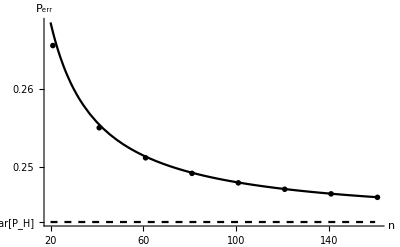

```mathematica
averplot=Show[ListPlot[Perrexactlist,PlotTheme->"Monochrome"],Plot[17/70+18/(35 n),{n,20,160},PlotTheme->"Monochrome"],Plot[17/70,{n,20,160},PlotTheme->"Monochrome",PlotStyle->Dashed],AxesLabel->{Style["n",Medium],Style["P_err",Medium]},Ticks->{{20,40,60,80,100,120,140,160},{0.24,{17/70,OverBar["P_H"]},0.25,0.26,0.27,0.28}},AxesOrigin->{20,0.24},PlotRange->All]
```